## cylindrical nanoscale mosfet compact model -- tunneling current approximation

### physical parameters

```mathematica
e=1.60218 10^-19;(*unit charge[C]*)
kB=1.38066 10^-23;(*Boltzmann constant[J/K]*)h=6.62607 10^-34;(*Planck's constant[Js]*)
hbar=h/(2 π);(*[Js]*)
T=300;(*temperature[K]*)
ϵ0=8.85418 10^-12;(*permittivity in vaccum[F/m]*)vt=(kB T)/e;(*thermal voltage[V]*)
m0=9.10938 10^-31;(*effective mass of electron in vaccum[kg]*)nm=10^-9;
ϵox=3.9 ϵ0;(*permittivity of oxide[F/m]*)
ϵsi=11.8 ϵ0;(*permittivity of silicon according to SILVACO[F/m]*)mt=0.19 m0;(*transverse effective mass of electron in SILICON[kg]*)
ml=0.916 m0;(*longitudinal effective mass of electron in SILICON[kg]*)
mr=2 (ml^-1+mt^-1)^-1;(*effective mass along radius direction in cross section in SILICON[kg]*)
GWF=4.5;(*workfunction of gate material from SILVACO[eV]*)CEA=4.17;(*electron affinity of channel material from SILVACO[eV]*)
wgc=GWF-CEA;(*workfunction difference between gate and channel[V]*)
wfb=0;(*conduction band edge under flat-band condition*)vbi=0.73;(*built-in voltage*)
Eg=0.54;(*fitting parameter*)
```

### device structure parameters

```mathematica
R=1 nm;(*radius of cross-section*)
Tox=0.5 nm;(*oxide thickness*)Cox[r_,tox_]:=2 π (ϵox)/Log[1+tox/r];(*capacitance of cylinder per unit length (F/m)*)
L=9 nm;(*Length of channel*)
```

### bias parameters

```mathematica
VGS0=0;
VGS2=0.2;
VGS5=0.5;
VGS8=0.8;
VDS=0.8;
```

### subbands parameters

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
valleykxky=4;(*4-fold degeneracy*)valleykz=2;(*2-fold degeneracy*)subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

$Aborted

### Fermi Integral

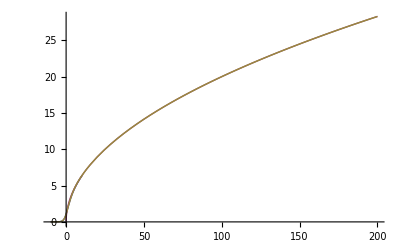

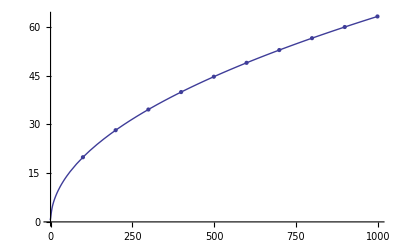

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

## potential distribution along channel

### characteristics parameters

```mathematica
γ=Sqrt[4/α]/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2;
ugzero[vbi_,vgs_]:=(vbi-vgs+wgc-wfb)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
ugLg[vbi_,vgs_,vds_]:=(vbi-vgs+wgc-wfb+vds)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
```

### deltaUG along channel

```mathematica
ug[vbi_,vgs_,vds_,z_]:=1/Sinh[γ L] (ugzero[vbi,vgs] Sinh[γ (L-z)]+ugLg[vbi,vgs,vds] Sinh[γ z])
aug[vbi_,vgs_,vds_,z_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ (L-z)]+Sinh[γ z])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ z]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))
Maug[vbi_,vgs_,vds_,z_]:=If[Re[aug[vbi,vgs,vds,z]]≤0,Re[aug[vbi,vgs,vds,z]],0]
```

### potential distribution

```mathematica
ϕ[vbi_,vgs_,vds_,r_,z_]:=WS-ug[vbi,vgs,vds,z] (1-r^2/R^2)/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
```

### the lowest energy level

```mathematica
Eq01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
E01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
```

### position of barrier top

```mathematica
zmax[vbi_,vgs_,vds_]:=-1/(2 γ) Log[B/A]/.A->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])/.B->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[-γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])
```

### smoothing function

```mathematica
SF[vgs_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4]]-ν)])^-1/.μ->0.6/.ν->-3
```

### DIBL effect involved deltaUG

```mathematica
DIBLUG[vbi_,vgs_,vds_]:=Re[SF[vgs] Maug[vbi,vgs,vds,zmax[vbi,vgs,vds]]]+U[vgs]
```

## approximation of transit coefficient

### position of the lowest energy of the lowest energy level along channel

```mathematica
zzMAX[vgs_]:=Solve[E01[vbi,vgs,VDS,z]==Eq01[vbi, vgs, VDS, 0],z][[3,1,2]]
zzMAX[VGS0]
FindRoot[E01[vbi,VGS0,VDS,z]==Eq01[vbi, VGS0, VDS, 0],{z,L}][[1,2]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧

8.60032×10^-9

### equal difference along channel

#### left hand side

```mathematica
deltazLHS[vgs_,vds_,n_]:=zmax[vbi,vgs,vds]/n
deltazLHS[VGS0,VDS,3]
```

1.41293×10^-9

#### right hand side

```mathematica
deltazRHS[vgs_,vds_,n_]:=(zzMAX[vgs]-zmax[vbi,vgs,vds])/n
deltazRHS[VGS0,VDS,3]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

1/3 (-4.23879×10^-9+Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧)

### rectanglar areasquare approximation for potential distribution

```mathematica
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,deltazLHS[vgs,vds,3]]/;0≤z<=deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,2 deltazLHS[vgs,vds,3]]/;deltazLHS[vgs,vds,3]≤z≤2 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,3 deltazLHS[vgs,vds,3]]/;2 deltazLHS[vgs,vds,3]≤z≤3 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]]/;zmax[vbi,vgs,vds]≤z≤zmax[vbi,vgs,vds]+deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]+deltazLHS[vgs,vds,3]]/;zmax[vbi,vgs,vds]+ deltazLHS[vgs,vds,3]≤z≤zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3]]/;zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3]≤z≤zmax[vbi,vgs,vds]+3 deltazLHS[vgs,vds,3];
```

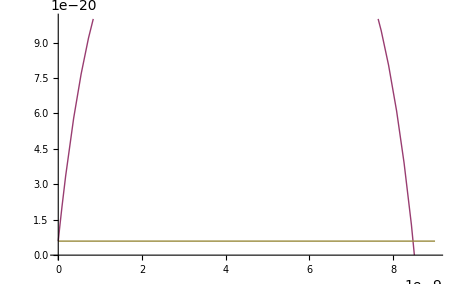

```mathematica
Plot[{stepE01[VGS0,VDS,z],E01[vbi,VGS0,VDS,z],E01[vbi,VGS0,VDS,0]},{z,0,L},PlotRange->{{0,L},{0,1 10^-19}}]
```

## check

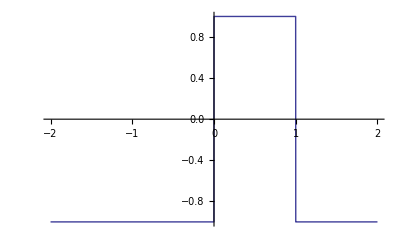

```mathematica
step[x_]:=-1/;x<=0;
step[x_]:=1/;0<=x<=1;
step[x_]:=-1/;1<=x;
Plot[step[x],{x,-2,2}]
```

```mathematica
E01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]+2 deltazRHS[VGS0,VDS,3]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (4.76121×10^-9-2/3 (-4.23879×10^-9+Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧))]-0.538571 Sinh[1.0762×10^9 (4.23879×10^-9+2/3 (-4.23879×10^-9+Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧))]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (4.76121×10^-9-2/3 (-4.23879×10^-9+Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧))]-0.538571 Sinh[1.0762×10^9 (4.23879×10^-9+2/3 (-4.23879×10^-9+Solve[1.1217×10^-19-1.60218×10^-19 (-0.33-0.000305015 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z]))+1.55743×10^-23 (-0.306928 Sinh[1.0762×10^9 (9/1000000000-z)]-0.538571 Sinh[1.0762×10^9 z])==5.93386×10^-21,z]⟦3,1,2⟧))])

```mathematica
Plot[stepE01[VGS0,VDS,zmax[vbi,VGS0,VDS]],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]
Plot[E01z04[VGS0,VDS],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]
Plot[TFApprox04[VGS0,VDS,Ez],{Ez,0,Eq01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]]}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

Plot::plln: Limiting value 4.23879×10^-9 + 1/3\ (-4.23879×10^-9 + Solve[1.1217×10^-19 + Times[« 2 »] + Times[« 2 »] == 5.93386×10^-21, z] ⟦ 3, 1, 2 ⟧) in {z, zmax[vbi, VGS0, VDS], zmax[vbi, VGS0, VDS] + deltazRHS[VGS0, VDS, 3]} is not a machine-sized real number.

Plot[stepE01[VGS0,VDS,zmax[vbi,VGS0,VDS]],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Part::partw: Part 3 of Solve[1.1217×10^-19 - 1.60218×10^-19\ (-0.33 - 0.000305015\ (Times[« 2 »] + Times[« 2 »])) + 1.55743×10^-23\ (-0.306928\ Sinh[Times[« 2 »]] - 0.538571\ Sinh[Times[« 2 »]]) == 5.93386×10^-21, z] does not exist.

Plot::plln: Limiting value 4.23879×10^-9 + 1/3\ (-4.23879×10^-9 + Solve[1.1217×10^-19 + Times[« 2 »] + Times[« 2 »] == 5.93386×10^-21, z] ⟦ 3, 1, 2 ⟧) in {z, zmax[vbi, VGS0, VDS], zmax[vbi, VGS0, VDS] + deltazRHS[VGS0, VDS, 3]} is not a machine-sized real number.

Plot[E01z04[VGS0,VDS],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]

-Graphics-

```mathematica
FlatVoltage = 
   FindRoot[Eq01[vbi, vgs, VDS, 0] == 
            Eq01[vbi, vgs, VDS, zmax[vbi, vgs, VDS]], {vgs, 0}][[1, 2]]
E01z01[vgs_, vds_] := E01[vbi, vgs, vds, deltazLHS[vgs, vds, 3]]
E01z02[vgs_, vds_] := E01[vbi, vgs, vds, 2 deltazLHS[vgs, vds, 3]]
E01z03[vgs_, vds_] := E01[vbi, vgs, vds, zmax[vbi, vgs, vds]]
E01z04[vgs_, vds_] := E01[vbi, vgs, vds, zmax[vbi, vgs, vds]]
E01z05[vgs_, vds_] := E01[vbi, vgs, vds, 4 deltazLHS[vgs, vds, 3]]
E01z06[vgs_, vds_] := E01[vbi, vgs, vds, 5 deltazLHS[vgs, vds, 3]]
TFApprox01[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z01[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 0, deltazLHS[vgs, vds, 3]}]], 0]
TFApprox02[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z02[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, deltazLHS[vgs, vds, 3], 2 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox03[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z03[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 2 deltazLHS[vgs, vds, 3], 3 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox04[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z04[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 3 deltazLHS[vgs, vds, 3], 4 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox05[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z05[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 4 deltazLHS[vgs, vds, 3], 5 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox06[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z06[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 5 deltazLHS[vgs, vds, 3], 6 deltazLHS[vgs, vds, 3]}]], 0]
```

1.05985

```mathematica
0.514249
```

0.514249

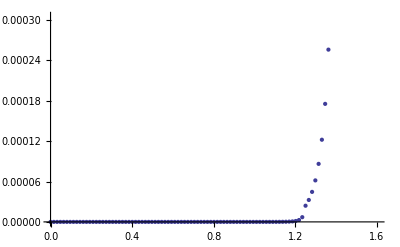

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {8.47004558486535×10^-9}. NIntegrate obtained 2.92652×10^-18 + 3.48277×10^-21\ ⅈ and 6.25132×10^-24 for the integral and error estimates.

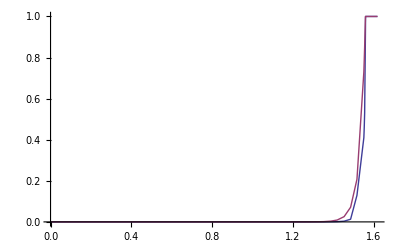

```mathematica
Show[ListPlot[Table[{Ez, Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]], 0.01 e}]], Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1}}]]
Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TF[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1}}]
```

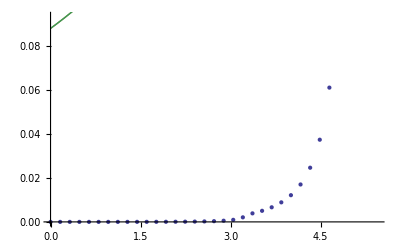

-Graphics-

```mathematica
NIntegrate::slwcon :  "Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/NIntegrate/slwcon\", ButtonNote -> \"NIntegrate::slwcon\"]\)"
```

Message::name: Message name NIntegrate is not of the form symbol::name or symbol::name::language.

NIntegrate::(slwcon:Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small. )

```mathematica
NIntegrate::ncvb :  "NIntegrate failed to converge to prescribed accuracy after \!\(9\) recursive bisections in \!\(z\) near \!\({z}\) = \!\({5.569582607143114`15.954589770191005*^-9}\). NIntegrate obtained \!\(1.044299386555847`*^-18 + \(\(3.2075695919549153`*^-21\\ ⅈ\)\)\) and \!\(7.429186200049437`*^-24\) for the integral and error estimates. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/NIntegrate/ncvb\", ButtonNote -> \"NIntegrate::ncvb\"]\)"
```

Message::name: Message name NIntegrate :: (ncvb : « 495 ») is not of the form symbol::name or symbol::name::language.

NIntegrate::(ncvb:NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.56958260714311×10^-9}. NIntegrate obtained 1.0443×10^-18 + 3.20757×10^-21\ ⅈ and 7.42919×10^-24 for the integral and error estimates. )

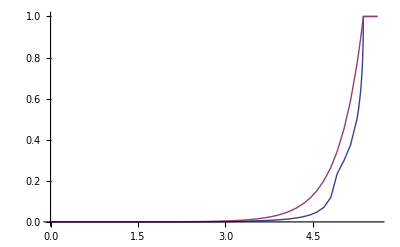

-Graphics-

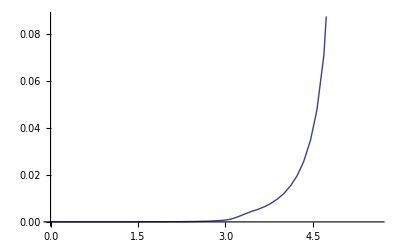

-Graphics-

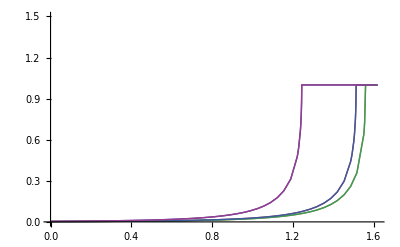

```mathematica
Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1.5}}]
```

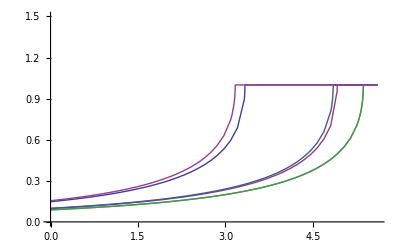

-Graphics-

## alternative approach of transition coefficient

### position of the lowest energy level in source

```mathematica
z01[vgs_,vds_,Ez_]:=Re[1/γ Log[C01]/.C01->(-(b3-Ez)-Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[vbi,vgs]/.a2->-(η01/2) ugzero[vbi,vgs]/Sinh[γ L] (Cosh[γ L]-ugLg[vbi,vgs,vds]/ugzero[vbi,vgs])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R,Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4]]/.WS->vgs-wgc+wfb]
z02[vgs_,vds_,Ez_]:=Re[1/γ Log[C02]/.C02->(-(b3-Ez)+Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[vbi,vgs]/.a2->-(η01/2) ugzero[vbi,vgs]/Sinh[γ L] (Cosh[γ L]-ugLg[vbi,vgs,vds]/ugzero[vbi,vgs])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R,Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4]]/.WS->vgs-wgc+wfb]
z01[VGS0,VDS,Eq01[vbi, VGS0, VDS, 0]](*SHOULD BE ELECTED*)
z02[VGS0,VDS,Eq01[vbi, VGS0, VDS, 0]]
```

8.47744×10^-9

-1.69184×10^-23

### slide the potential distribution into N pieces

#### difference between each piece

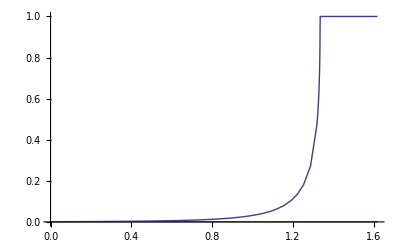

```mathematica
deltaz[vgs_,vds_,N_]:=z01[vgs,vds,Eq01[vbi, vgs,vds, 0]]/N
transcoef[vgs_,vds_,Ez_,N_,n_]:=If[vgs<FlatVoltage,Exp[-2/hbar Sqrt[2 mt] Re[Integrate[Sqrt[Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,N]]- Ez - E01[vbi, vgs, vds, 0]],{z,n deltaz[vgs,vds,N],(n+1) deltaz[vgs,vds,N]}]]],1]
Plot[{transcoef[VGS0,VDS,Ez,5,0],transcoef[VGS0,VDS,0,5,0],transcoef[VGS0,VDS,0,5,0]+Ez^2},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.47312×10^-12}. NIntegrate obtained 2.60417×10^-18 + 2.30351×10^-21\ ⅈ and 9.95637×10^-24 for the integral and error estimates.

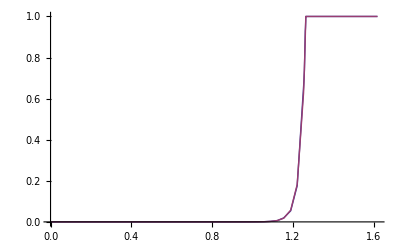

```mathematica
totaltransco[vgs_,vds_,Ez_,N_]:=Product[transcoef[vgs,vds,Ez,N,n],{n,0,20}]
Plot[{totaltransco[VGS2,VDS,Ez,20],Exp[-2/hbar Sqrt[2 mt] TF[VGS2, VDS, Ez]]},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,1}]
```

## total current

### tunel current

```mathematica
approxtunnelcurrentapprox[vgs_,vds_,st_]:=If[vgs<FlatVoltage,Re[e/(π hbar) st[[1,1]] NIntegrate[totaltransco[vgs,vds,Ez,20]/(1+Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,0,-Eq01[vbi,vgs,vds,0]+Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]}]],0]
Export["/home/tei/mathematica/anaertunnelcurrent_app.txt",Table[Re[{vgs,approxtunnelcurrentapprox[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.8417×10^-20}. NIntegrate obtained 2.38442×10^-35 and 1.8098×10^-40 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.78633×10^-20}. NIntegrate obtained 2.91452×10^-35 and 9.66418×10^-41 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.73097×10^-20}. NIntegrate obtained 3.56694×10^-35 and 7.06306×10^-41 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Export::nodir: Directory "C:\\home\\tei\\mathematica\\" does not exist.

Export::noopen: Cannot open "/home/tei/mathematica/anaertunnelcurrent_app.txt".

### total current

```mathematica
approxTatolCurrent[vgs_,vds_,st_]:=Re[1/(1+Exp[25(vgs-FlatVoltage+.2)]) approxtunnelcurrentapprox[vgs,vds,st]+1/(1+Exp[-25 (vgs-FlatVoltage+.2)]) DIBLSINGLEBANDCURRENT[vbi,vgs,vds,st]]
```

### plot

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.84158×10^-20}. NIntegrate obtained 2.38539×10^-35 and 1.81084×10^-40 for the integral and error estimates.

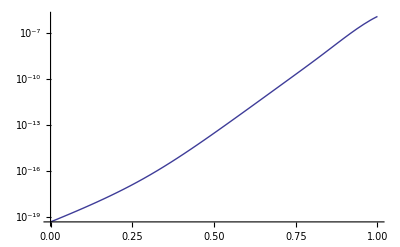

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.84158×10^-20}. NIntegrate obtained 2.38539×10^-35 and 1.81084×10^-40 for the integral and error estimates.

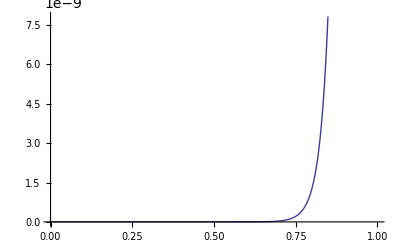

```mathematica
LogPlot[approxTatolCurrent[vgs,VDS,subbandtable],{vgs,0,1}]
Plot[approxTatolCurrent[vgs,VDS,subbandtable],{vgs,0,1}]
(*Export["/home/tei/mathematica/anatotalcurrent.txt",Table[Re[{vgs,approxTatolCurrent[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {5.84158×10^-20}. NIntegrate obtained 2.38539×10^-35 and 1.81084×10^-40 for the integral and error estimates.

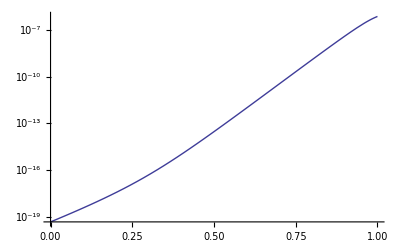

```mathematica
LogPlot[approxtunnelcurrentapprox[vgs,VDS,subbandtable],{vgs,0,1}]
```

## parabolic approximation of transmission coefficient

### transmission coefficient of each segment

#### segment factor

```mathematica
A[vgs_,vds_]:=-2/hbar Sqrt[2 mt] (deltaz[vgs,vds,20])
S[vgs_,vds_,n_]:=Sqrt[Eq01[vbi, vgs,vds,n deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0]]
```

```mathematica
A[VGS0,VDS]
Sum[S[VGS0,VDS,m],{m,1,N}]/.N->19
Sum[1/S[VGS0,VDS,m],{m,1,19}]
```

-4.7296×10^9

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

FactorSquareFree::lrgexp: Exponent is out of bounds for function FactorSquareFree.

General::stop: Further output of FactorSquareFree :: lrgexp will be suppressed during this calculation.

6.79398×10^-9

5.43635×10^10

#### approximation of root function of transmission expression

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {8.47004558486535×10^-9}. NIntegrate obtained 2.92652×10^-18 + 3.48277×10^-21\ ⅈ and 6.25132×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {8.47006398997755×10^-9}. NIntegrate obtained 2.92656×10^-18 + 3.48269×10^-21\ ⅈ and 6.25817×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {8.4521895472009×10^-9}. NIntegrate obtained 2.88243×10^-18 + 3.5533×10^-21\ ⅈ and 8.20265×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

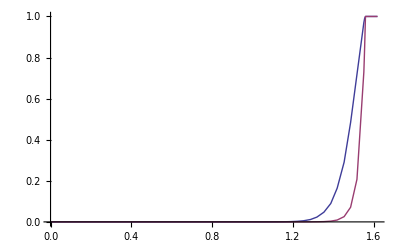

```mathematica
transcoef03[vgs_,vds_,Ez_,n_]:=If[Ez<Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0],Re[Exp[-2/hbar Sqrt[2 mt] deltaz[vgs,vds,20] (Sqrt[Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0]]- Ez/(2 Sqrt[Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0]])-0.5 Ez^2/ (Sqrt[Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0]]^3))]],1]
transmissioncoff[vgs_,vds_,Ez_]:=Product[transcoef03[vgs,vds,Ez,n],{n,0,20}]
Plot[{transmissioncoff[VGS0,VDS,Ez],Exp[-2/hbar Sqrt[2 mt] TF[VGS0, VDS, Ez]],totaltransco03[VGS0,VDS,Ez,20]},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,1}]
```

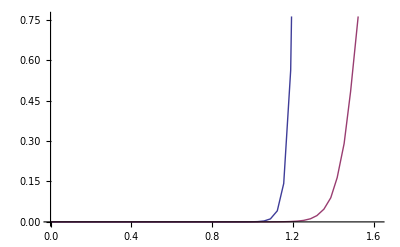

```mathematica
approxtotaltransco[vgs_,vds_,Ez_]:=Exp[-2/hbar Sqrt[2 mt] deltaz[vgs,vds,20] (Sum[S[vgs,vds,m],{m,1,19}]-Ez/2 Sum[1/S[vgs,vds,m],{m,1,19}]-Ez^2/2 Sum[1/S[vgs,vds,m]^3,{m,1,19}])]
Plot[{approxtotaltransco[VGS0,VDS,Ez],transmissioncoff[VGS0,VDS,Ez]},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}]
```

## tunnel current

### parabolic approximation

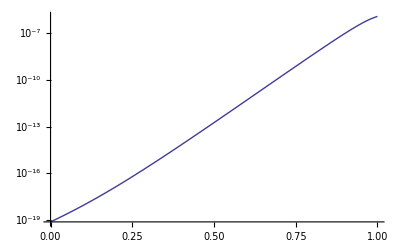

```mathematica
parabolicapproxtunnelcurrent[vgs_,vds_,st_]:=If[vgs<FlatVoltage,Re[e/(π hbar) st[[1,1]] NIntegrate[transmissioncoff[vgs,vds,Ez]/(1+Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,0,-Eq01[vbi,vgs,vds,0]+Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]}]],0]
LogPlot[parabolicapproxtunnelcurrent[vgs,VDS,subbandtable],{vgs,0,1}]
```

### current approximation(Boltzmman distribution)

```mathematica
partparabolicapproxitunnelcurrent[vgs_,vds_,st_,m_]:=If[vgs<FlatVoltage,Re[e/(π hbar)st[[1,1]] NIntegrate[Product[transcoef03[vgs,vds,Ez,i],{i,m,20-m}]/(Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,Eq01[vbi, vgs,vds,m deltaz[vgs,vds,20]],Eq01[vbi, vgs,vds,(m+1) deltaz[vgs,vds,20]]}]] ,0]
partlayerparabolicapproxitunnelcurrent[vgs_,vds_,st_,i_]:=If[vgs<FlatVoltage,Re[e/(π hbar)st[[1,1]] NIntegrate[Exp[-2/hbar Sqrt[2 mt] (deltaz[vgs,vds,20]) (Sum[S[vgs,vds,m],{m,i,20-i}]-Ez Sum[1/(2 S[vgs,vds,m]),{m,i,20-i}]-Ez^2 Sum[1/(2 S[vgs,vds,m]^3),{m,i,20-i}])]/(Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,Eq01[vbi, vgs,vds,i deltaz[vgs,vds,20]],Eq01[vbi, vgs,vds,(i+1) deltaz[vgs,vds,20]]}]] ,0]
LogPlot[{Sum[
partparabolicapproxitunnelcurrent[vgs,VDS,subbandtable,m],{m,1,9}],Sum[partlayerparabolicapproxitunnelcurrent[vgs,VDS,subbandtable,i],{i,1,9}],parabolicapproxtunnelcurrent[vgs,VDS,subbandtable]},{vgs,0,1}]
```

$Aborted

### current approximation using Error Function

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

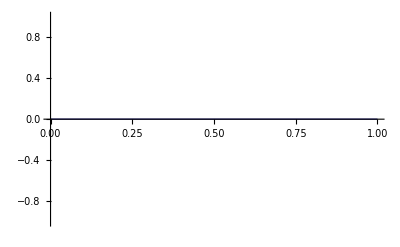

```mathematica
partparabolicapproxerftunnelcurrent[vgs_,vds_,st_,m_]:=If[vgs<FlatVoltage,Re[e/(π hbar)st[[1,1]] Exp[-2/hbar Sqrt[2 mt] deltaz[vgs,vds,20]] 1/2 Sqrt[π/Sum[1/(2 S[vgs,vds,i]^3),{i,m,20-m}]] Exp[Sum[S[vgs,vds,i],{i,m,20-m}]+Eq01[vbi,vgs,vds,0]/(2/hbar deltaz[vgs,vds,20] Sqrt[2 mt] kB T)+(0.5 Sum[1/S[vgs,vds,i],{i,m,20-m}]+1/(2/hbar deltaz[vgs,vds,20] Sqrt[2 mt] kB T))^2/(4 Sum[1/(2 S[vgs,vds,i]^3),{i,m,20-m}])] Erf[(Sum[1/(2 S[vgs,vds,i]),{i,m,20-m}]+1/(2/hbar deltaz[vgs,vds,20] Sqrt[2 mt] kB T)+2  Sum[1/(2 S[vgs,vds,i]^3),{i,m,20-m}] )/(2 Sqrt[Sum[1/(2 S[vgs,vds,i]^3),{i,m,20-m}]]) (Eq01[vbi, vgs,vds,(m+1) deltaz[vgs,vds,20]]-Eq01[vbi, vgs,vds,m deltaz[vgs,vds,20]])]],0]
Plot[Sum[partparabolicapproxerftunnelcurrent[vgs,VDS,subbandtable,m],{m,1,9}],{vgs,0,1}]
```